```mathematica
Manipulate[Plot[{(1-CDF[NormalDistribution[0,1],Abs[L]/(√(1-s))])/(√(2π)s^(3/2))Abs[L] ⅇ^(-L^2/(2s)),(1-CDF[NormalDistribution[0,1],Abs[L]/(√(1-s))])/(√(2π))Abs[L] ⅇ^(-L^2/(2s))},{s,0,1},PlotRange->Full],{L,1,4}]
```

```mathematica
∫_0^1 (1-CDF[NormalDistribution[0,1],Abs[L]/(√(1-s))])/(√(2π))Abs[L] ⅇ^(-L^2/(2s))ⅆs
```

∫_0^1 (ⅇ^(-L^2/(2 s)) Abs[L] (1-1/2 Erfc[-Abs[L]/(√2 √(1-s))]))/(√(2 π))ⅆs

```mathematica
D[(1-CDF[NormalDistribution[0,1],Abs[L]/(√(1-s))])/(√(2π)s^(3/2))Abs[L] ⅇ^(-L^2/(2s)),s]
```

-(ⅇ^(-L^2/(2 s)-Abs[L]^2/(2 (1-s))) Abs[L]^2)/(4 π (1-s)^(3/2) s^(3/2))+(ⅇ^(-L^2/(2 s)) L^2 Abs[L] (1-1/2 Erfc[-Abs[L]/(√2 √(1-s))]))/(2 √(2 π) s^(7/2))-(3 ⅇ^(-L^2/(2 s)) Abs[L] (1-1/2 Erfc[-Abs[L]/(√2 √(1-s))]))/(2 √(2 π) s^(5/2))

```mathematica
Solve[-(ⅇ^(-L^2/(2 s)-Abs[L]^2/(2 (1-s))) Abs[L]^2)/(4 π (1-s)^(3/2) s^(3/2))+(ⅇ^(-L^2/(2 s)) L^2 Abs[L] (1-1/2 Erfc[-Abs[L]/(√2 √(1-s))]))/(2 √(2 π) s^(7/2))-(3 ⅇ^(-L^2/(2 s)) Abs[L] (1-1/2 Erfc[-Abs[L]/(√2 √(1-s))]))/(2 √(2 π) s^(5/2)) == 0, s]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-(ⅇ^(-L^2/(2 s)-Abs[L]^2/(2 (1-s))) Abs[L]^2)/(4 π (1-s)^(3/2) s^(3/2))+(ⅇ^(-L^2/(2 s)) L^2 Abs[L] (1-1/2 Erfc[-Abs[L]/(√2 √(1-s))]))/(2 √(2 π) s^(7/2))-(3 ⅇ^(-L^2/(2 s)) Abs[L] (1-1/2 Erfc[-Abs[L]/(√2 √(1-s))]))/(2 √(2 π) s^(5/2))==0,s]

```mathematica
∫_0^1 (2(1-CDF[NormalDistribution[0,1],Abs[L]/(√(1-s))]))/(√(2π)s^(3/2))Abs[L] ⅇ^(-L^2/(2s))ⅆs/. L-> -3 //N
```

1.97318×10^-9

```mathematica
∫_0^1 (2(1-CDF[NormalDistribution[0,1],Abs[3]/(√(1-s))]))/(√(2π)s^(3/2))Abs[3+0.5] ⅇ^((-(3+0.5)^2)/(2s))ⅆs//N
```

8.032×10^-11

```mathematica
∫_0^1 (2(1-CDF[NormalDistribution[0,1],Abs[4]/(√(1-s))]))/(√(2π)s^(3/2))Abs[3+0.5] ⅇ^((-(3+0.5)^2)/(2s))ⅆs//N
```

6.38178×10^-14

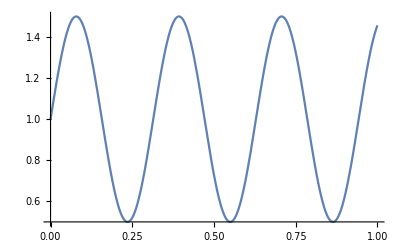

```mathematica
Plot[1 + 0.5Sin[20t],{t,0,1}]
```

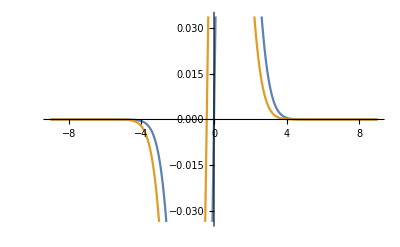

```mathematica
Plot[{x PDF[NormalDistribution[0,1 ],x],(x+0.4) PDF[NormalDistribution[0,1 ],x+0.4]},{x,-9,9}]
```

```mathematica
Manipulate[Plot[{x PDF[NormalDistribution[0,1 ],x]-(x+e) PDF[NormalDistribution[0,1 ],x+e]},{x,-9,9},PlotRange->{{-9,9},{-1,1}}],{e,0,1}]
```

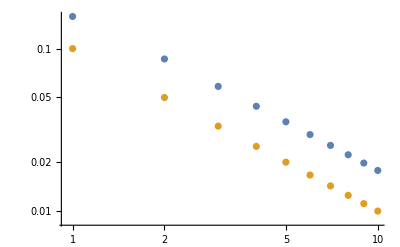

```mathematica
ListLogLogPlot[{Table[NMaximize[x PDF[NormalDistribution[0,1 ],x]-(x+1/n) PDF[NormalDistribution[0,1 ],x+1/n],x][[1]],{n,1,10}],
Table[0.1/n,{n,1,10}]}]
```

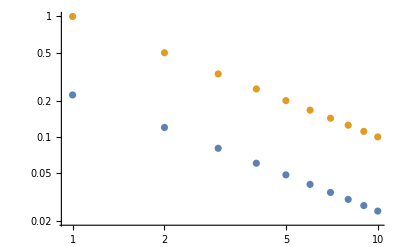

```mathematica
ListLogLogPlot[{Table[NMaximize[  PDF[NormalDistribution[0,1/(√n) ],x]-PDF[NormalDistribution[0,1/(√n) ],x+1/n^2],x][[1]],{n,1,10}],
Table[1/n,{n,1,10}]}]
```

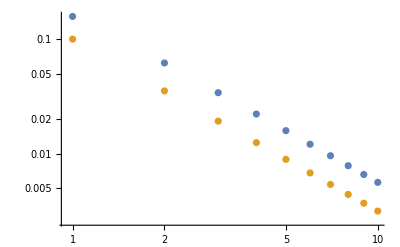

```mathematica
ListLogLogPlot[{Table[NMaximize[x  PDF[NormalDistribution[0,1/(√n) ],x]-(x+1/n^2)PDF[NormalDistribution[0,1/(√n) ],x+1/n^2],x][[1]],{n,1,10}],
Table[0.1/n^(3/2),{n,1,10}]}]
```

```mathematica
D[x PDF[NormalDistribution[0,1/(√n)],x],{x,1}]
```

(ⅇ^(-(n x^2)/2) √n)/(√(2 π))-(ⅇ^(-(n x^2)/2) n^(3/2) x^2)/(√(2 π))

```mathematica
D[x PDF[NormalDistribution[0,1/(√n)],x],{x,2}]
```

-ⅇ^(-(n x^2)/2) n^(3/2) √(2/π) x+(√n x (-ⅇ^(-(n x^2)/2) n+ⅇ^(-(n x^2)/2) n^2 x^2))/(√(2 π))

```mathematica
Solve[-ⅇ^(-(n x^2)/2) n^(3/2) √(2/π) x+(√n x (-ⅇ^(-(n x^2)/2) n+ⅇ^(-(n x^2)/2) n^2 x^2))/(√(2 π))== 0,x]
```

{{x→0},{x→-(√3)/(√n)},{x→(√3)/(√n)}}

```mathematica
(ⅇ^(-(n x^2)/2) √n)/(√(2 π))-(ⅇ^(-(n x^2)/2) n^(3/2) x^2)/(√(2 π))/.{{x->0},{x->-(√3)/(√n)},{x->(√3)/(√n)}}
```

{(√n)/(√(2 π)),-(√n √(2/π))/ⅇ^(3/2),-(√n √(2/π))/ⅇ^(3/2)}

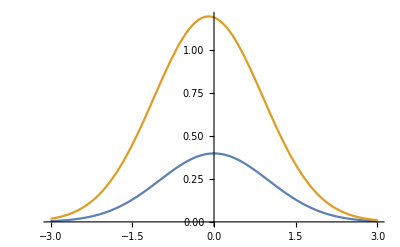

```mathematica
Plot[{PDF[NormalDistribution[0,1],x],3PDF[NormalDistribution[0,1],x+0.1]},{x,-3,3}]
```

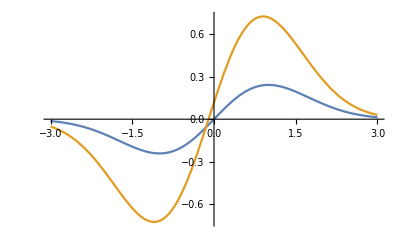

```mathematica
Plot[{x PDF[NormalDistribution[0,1],x],3(x+0.1)PDF[NormalDistribution[0,1],x+0.1]},{x,-3,3}]
```

```mathematica
FourierTransform[(x-μ)PDF[NormalDistribution[0,1/(√n)],x-μ],x,s,FourierParameters->{0, -2*Pi}]
```

-(2 ⅈ ⅇ^(-(2 π s (π s+ⅈ n μ))/n) π s)/n

```mathematica
ComplexExpand[Re[-(2 ⅈ ⅇ^(-(2 π s (π s+ⅈ n μ))/n) π s)/n]]
```

-(2 ⅇ^(-(2 π^2 s^2)/n) π s Sin[2 π s μ])/n

```mathematica
Plo\
```

```mathematica
Series[Sin[x],{x,0,3}]
```

x-x^3/6+O[x]^4

```mathematica
Sin[2π]
```

0

```mathematica
∑_(j=1)^∞ j Exp[-2 π^2 j^2]//N
```

2.67529×10^-9

```mathematica
Cos[2π]
```

1

```mathematica
Sin[2π 1(1+0.05)]
```

0.309017

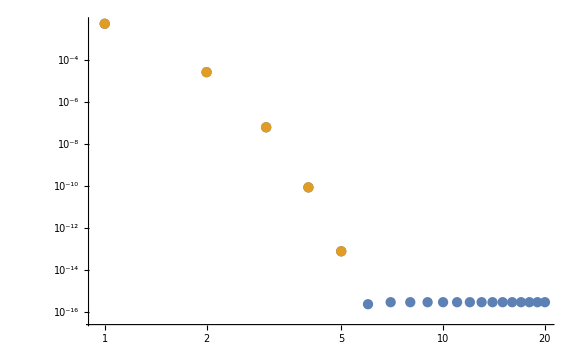

```mathematica
ListLogLogPlot[{Table[Abs[Sin[2π 1(1+0.05)]-∑_(i=1)^n (-1)^(i+1)/((2i -1 )!)(2π *0.05)^(2i -1)],{n,1,20}],
Table[Abs[(-1)^(n+1+1)/((2(n+1) -1 )!)(2π *0.05)^(2(n+1) -1)],{n,1,5}]}]
```

```mathematica
∑_(i=1)^∞ (-1)^(i+1)/((2i -1 )!)(2π 9*0.4)^(2i -1)
```

-0.587785

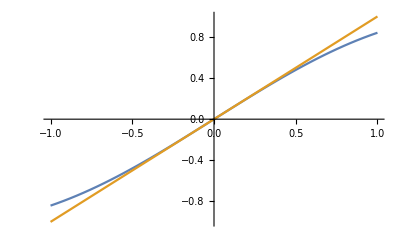

```mathematica
Plot[{Sin[x],x},{x,-1,1}]
```

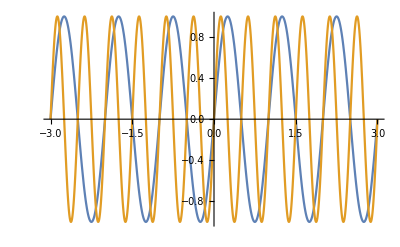

```mathematica
Plot[{Sin[2π x],Sin[2π 2x]},{x,-3,3}]
```

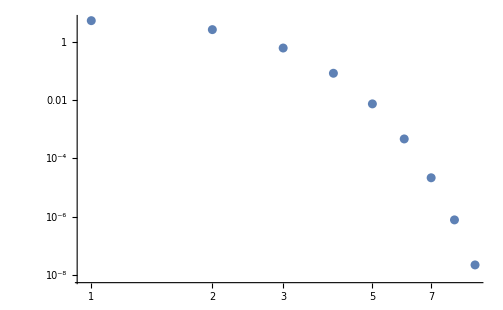

```mathematica
ListLogLogPlot[Table[(2π 0.5)^(2i-1)/((2i-1)!)//N,{i,2,10}]]
```

```mathematica
Plot[]
```

```mathematica
FourierTransform[(x-μ)^2 PDF[NormalDistribution[0,1/(√n)],x-μ],x,s,FourierParameters->{0, -2*Pi}]
```

(ⅇ^(-(2 π s (π s+ⅈ n μ))/n) (n-4 π^2 s^2))/n^2

```mathematica
ComplexExpand[Re[(ⅇ^(-(2 π s (π s+ⅈ n μ))/n) (n-4 π^2 s^2))/n^2]]//Simplify
```

(ⅇ^(-(2 π^2 s^2)/n) (n-4 π^2 s^2) Cos[2 π s μ])/n^2

```mathematica
(ⅇ^(-(2 π^2 s^2)/n) (n-4 π^2 s^2) Cos[2 π s μ])/n^2/. s-> 0
```

1/n

```mathematica
Table[N[∑_(k=-4*n)^(4*n) PDF[NormalDistribution[0,1/(√n)],k/(√n)]/(√n),20]-1,{n,1,40}]
```

{-2.9802584987335×10^-6,5.3505759801×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9,5.3505759821×10^-9}

```mathematica
g[t_]:=√(π/6+t)
```

```mathematica
Table[N[(n(∑_(k=-4*n)^(4*n) (g[2/n]/Floor[√n] k)^2 PDF[NormalDistribution[0,1/(√n)],g[2/n]/Floor[√n] k] g[2/n]/Floor[√n])/(∑_(k=-4*n)^(4*n) PDF[NormalDistribution[0,1/(√n)],g[2/n]/Floor[√n] k] g[2/n]/Floor[√n]))-1,20],{n,1,50}]
```

{-0.012532435079198150613,-0.039707531972229759313,-0.08718169263940910124,-3.2528948099751449232×10^-7,-2.5679231653618382211×10^-6,-0.000013155622249925000174,-0.000049361771564477756737,-0.00014692474116099621472,-3.3926315329382991171×10^-10,-2.1362000646131286645×10^-9,-1.0441941514864632413×10^-8,-4.1585568165670052103×10^-8,-1.3999313390566707683×10^-7,-4.0987800169029456649×10^-7,-1.0673971718803618432×10^-6,-7.3834661537504343222×10^-12,-3.031943799416578523×10^-11,-1.0914294817631421848×10^-10,-3.5046434791417767467×10^-10,-1.018480079262231215×10^-9,-2.7113931688251288771×10^-9,-6.680599122722349081×10^-9,-1.5367630380136955555×10^-8,-3.3251135171528046493×10^-8,-8.2056277358104384555×10^-13,-2.3745307814321347573×10^-12,-6.4065615294457261583×10^-12,-1.622318729585941825×10^-11,-3.8783042034196484156×10^-11,-8.7977678663765619843×10^-11,-1.9023987988978594165×10^-10,-3.9371462959820930601×10^-10,-7.8266157051903601341×10^-10,-1.499252637365464591×10^-9,-2.775463953208300889×10^-9,-2.1508879362329002276×10^-13,-4.8357548948903148366×10^-13,-1.0452724858223985497×10^-12,-2.1782923995879269124×10^-12,-4.3874974081654181415×10^-12,-8.5610388989645969112×10^-12,-1.6216336741277667994×10^-11,-2.9876226811335937264×10^-11,-5.3629760380459185366×10^-11,-9.3948750580102242259×10^-11,-1.6085069335872438444×10^-10,-2.6952106686243072967×10^-10,-4.4253300016936720303×10^-10,-9.0630042203973737959×10^-14,-1.7034833205860545459×10^-13}

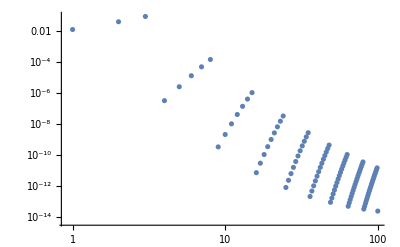

```mathematica
ListLogLogPlot[Table[N[Abs[(n(∑_(k=-4*n)^(4*n) (g[2/n]/Floor[√n] k)^2 PDF[NormalDistribution[0,1/(√n)],g[2/n]/Floor[√n] k] g[2/n]/Floor[√n])/(∑_(k=-4*n)^(4*n) PDF[NormalDistribution[0,1/(√n)],g[2/n]/Floor[√n] k] g[2/n]/Floor[√n]))-1],20],{n,1,100}]]
```

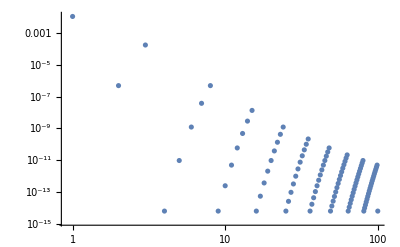

```mathematica
ListLogLogPlot[Table[N[Abs[(n(∑_(k=-4*n)^(4*n) (g[0]/Floor[√n] k)^2 PDF[NormalDistribution[0,1/(√n)],g[0]/Floor[√n] k] g[0]/Floor[√n])/(∑_(k=-4*n)^(4*n) PDF[NormalDistribution[0,1/(√n)],g[0]/Floor[√n] k] g[0]/Floor[√n]))-1],20],{n,1,100}]]
```

```mathematica
g[0]^3//N
```

0.378877

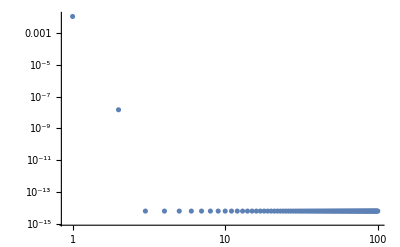

```mathematica
ListLogLogPlot[Table[N[Abs[(n(∑_(k=-4*n)^(4*n) (g[0]/(√n)k)^2 PDF[NormalDistribution[0,1/(√n)],g[0]/(√n)k] g[0]/(√n))/(∑_(k=-4*n)^(4*n) PDF[NormalDistribution[0,1/(√n)],g[0]/(√n)k] g[0]/(√n)))-1],20],{n,1,100}]]
```

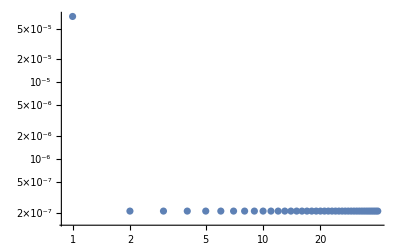

```mathematica
ListLogLogPlot[Table[N[Abs[(n(∑_(k=-4*n)^(4*n) (k/(√n))^2 PDF[NormalDistribution[0,1/(√n)],k/(√n)]/(√n))/(∑_(k=-4*n)^(4*n) PDF[NormalDistribution[0,1/(√n)],k/(√n)]/(√n)))-1],20],{n,1,40}]]
```

```mathematica
Table[N[(√((n∑_(k=-4*n)^(4*n) (k/(√n))^2 PDF[NormalDistribution[0,1/(√n)],k/(√n)]/(√n))/(∑_(k=-4*n)^(4*n) PDF[NormalDistribution[0,1/(√n)],k/(√n)]/(√n))))-1,20],{n,1,40}]
```

{-0.000036000734490851017922,-1.0561614161807462988×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7,-1.0561614153582881493×10^-7}

```mathematica
Table[N[∑_(k=-3*n)^(3*n) PDF[NormalDistribution[0,1/(√n)],k/n]/n-1,20],{n,1,40}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1+(√(2/π))/(5 ⅇ^(225/2))+(√(2/π))/(5 ⅇ^(2738/25))+(√(2/π))/(5 ⅇ^(5329/50))+(√(2/π))/(5 ⅇ^(2592/25))+(√(2/π))/(5 ⅇ^(5041/50))+(√(2/π))/(5 ⅇ^98)+(√(2/π))/(5 ⅇ^(4761/50))+(√(2/π))/(5 ⅇ^(2312/25))+(√(2/π))/(5 ⅇ^(4489/50))+(√(2/π))/(5 ⅇ^(2178/25))+(√(2/π))/(5 ⅇ^(169/2))+(√(2/π))/(5 ⅇ^(2048/25))+«25»+(√(2/π))/(5 ⅇ^(722/25))+(√(2/π))/(5 ⅇ^(1369/50))+(√(2/π))/(5 ⅇ^(648/25))+(√(2/π))/(5 ⅇ^(49/2))+(√(2/π))/(5 ⅇ^(578/25))+(√(2/π))/(5 ⅇ^(1089/50))+(√(2/π))/(5 ⅇ^(512/25))+(√(2/π))/(5 ⅇ^(961/50))+(√(2/π))/(5 ⅇ^18)+(√(2/π))/(5 ⅇ^(841/50))+(√(2/π))/(5 ⅇ^(392/25))+(√(2/π))/(5 ⅇ^(729/50))+«27».

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1+1/(2 √(13 π))+1/(ⅇ^117 √(13 π))+1/(ⅇ^(5929/52) √(13 π))+1/(ⅇ^(1444/13) √(13 π))+1/(ⅇ^(5625/52) √(13 π))+1/(ⅇ^(1369/13) √(13 π))+1/(ⅇ^(5329/52) √(13 π))+1/(ⅇ^(1296/13) √(13 π))+1/(ⅇ^(5041/52) √(13 π))+1/(ⅇ^(1225/13) √(13 π))+«29»+1/(ⅇ^(400/13) √(13 π))+1/(ⅇ^(117/4) √(13 π))+1/(ⅇ^(361/13) √(13 π))+1/(ⅇ^(1369/52) √(13 π))+1/(ⅇ^(324/13) √(13 π))+1/(ⅇ^(1225/52) √(13 π))+1/(ⅇ^(289/13) √(13 π))+1/(ⅇ^(1089/52) √(13 π))+1/(ⅇ^(256/13) √(13 π))+1/(ⅇ^(961/52) √(13 π))+«30».

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1+(√(2/(3 π)))/(3 ⅇ^(243/2))+(√(2/(3 π)))/(3 ⅇ^(3200/27))+(√(2/(3 π)))/(3 ⅇ^(6241/54))+(√(2/(3 π)))/(3 ⅇ^(338/3))+(√(2/(3 π)))/(3 ⅇ^(5929/54))+(√(2/(3 π)))/(3 ⅇ^(2888/27))+(√(2/(3 π)))/(3 ⅇ^(625/6))+(√(2/(3 π)))/(3 ⅇ^(2738/27))+(√(2/(3 π)))/(3 ⅇ^(5329/54))+(√(2/(3 π)))/(3 ⅇ^96)+(√(2/(3 π)))/(3 ⅇ^(5041/54))+«28»+(√(2/(3 π)))/(3 ⅇ^(98/3))+(√(2/(3 π)))/(3 ⅇ^(1681/54))+(√(2/(3 π)))/(3 ⅇ^(800/27))+(√(2/(3 π)))/(3 ⅇ^(169/6))+(√(2/(3 π)))/(3 ⅇ^(722/27))+(√(2/(3 π)))/(3 ⅇ^(1369/54))+(√(2/(3 π)))/(3 ⅇ^24)+(√(2/(3 π)))/(3 ⅇ^(1225/54))+(√(2/(3 π)))/(3 ⅇ^(578/27))+(√(2/(3 π)))/(3 ⅇ^(121/6))+«33».

General::stop: Further output of N::meprec will be suppressed during this calculation.

{-0.00027064071002850421206,-2.7641180916663277824×10^-6,-2.7437098762800575089×10^-8,-2.7633894890952523779×10^-10,-2.8230863035471133152×10^-12,-2.916800932536143227×10^-14,-3.0403438547997866994×10^-16,-3.1913879056038138603×10^-18,-3.3689445855860894714×10^-20,-3.572969999127682445×10^-22,-3.8041167601184522567×10^-24,-4.0635844635888895414×10^-26,-4.3530321212441143867×10^-28,-4.6745297511283808331×10^-30,-5.0305354912211736189×10^-32,-5.4238901131973861827×10^-34,-5.8578240642134166614×10^-36,-6.3359741071791747694×10^-38,-6.8624078172732170182×10^-40,-7.4416549395092115475×10^-42,-8.0787450986845490239×10^-44,-8.779251683051273302×10^-46,-9.5493419579374058457×10^-48,-1.0395833642357850093×10^-49,-1.13262583232833887×10^-51,-1.234893220320922×10^-53,-1.3473034786473×10^-55,-1.47086962148×10^-57,-1.606709407×10^-59,-1.7560561×10^-61,-1.92027×10^-63,-2.101×10^-65,-2.3×10^-67,-3.×10^-69,0.,0.,0.,0.,0.,0.}

```mathematica
Manipulate[LogLogPlot[Exp[-2 π^2 n^(2α-1)],{n,1,50}],{α,1/2,2}]
```

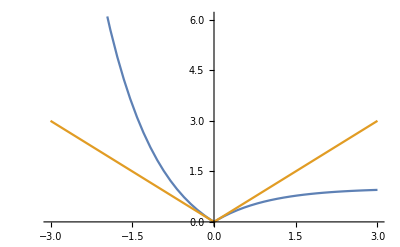

```mathematica
Plot[{Abs[1-ⅇ^-x],Abs[x]},{x,-3,3}]
```